### Full Generality

```mathematica
α = ({{α1}, {α2}, {α3}});
c0=({{c01}, {c02}, {c03}});
c1=({{c11}, {c12}, {c13}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{0, 0, 0}, {A021, 0, 0}, {A031, A032, 0}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] + μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0
A021 h μ | 1 | 0
A031 h μ | A032 h μ | 1)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+(B021 I10 σ^2)/h
U+((B031+B032) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

(U
U-A021 h U μ+(B021 I10 σ^2)/h
U+U (-A031 h μ+A021 A032 h^2 μ^2)+((B031+B032) I10 σ^2)/h-A032 h μ (U+(B021 I10 σ^2)/h))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ (U α1+α2 (U-A021 h U μ+1/2 B021 (W+Z/(√3)) σ^2)+α3 (U+U (-A031 h μ+A021 A032 h^2 μ^2)+1/2 (B031+B032) (W+Z/(√3)) σ^2-A032 h μ (U+1/2 B021 (W+Z/(√3)) σ^2)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U (1+h α1 μ+h α2 μ+h α3 μ-A021 h^2 α2 μ^2-A032 h^2 α3 μ^2+h α3 μ (-A031 h μ+A021 A032 h^2 μ^2))+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+1/2 B021 h (W+Z/(√3)) α2 μ σ^2+1/2 (B031+B032) h (W+Z/(√3)) α3 μ σ^2-1/2 A032 B021 h^2 (W+Z/(√3)) α3 μ^2 σ^2

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U (1+h α1 μ+h α2 μ+h α3 μ-A021 h^2 α2 μ^2-A032 h^2 α3 μ^2+h α3 μ (-A031 h μ+A021 A032 h^2 μ^2))

1+h α1 μ+h α2 μ+h α3 μ-A021 h^2 α2 μ^2-A032 h^2 α3 μ^2+h α3 μ (-A031 h μ+A021 A032 h^2 μ^2)

```mathematica
stableeq = G/.  {μ -> z/h}
```

1+z α1+z α2-A021 z^2 α2+z α3-A032 z^2 α3+z (-A031 z+A021 A032 z^2) α3

Two Stage
A021 -> 1 to ensure c0[end] = 1
a1 + a2 = 1 -> a1 = 1-a2

```mathematica
tsstab = Simplify[1+z α1+z α2-A021 z^2 α2 /. {A021->1,α1->1-α2}]
```

1+z-z^2 α2

```mathematica
Solve[1+z-z^2 α2 == 1,z]
Roots[1+z-z^2 α2 == -1,z]
```

z==0||z==1/α2

z==(1+√(1+8 α2))/(2 α2)||z==(1-√(1+8 α2))/(2 α2)

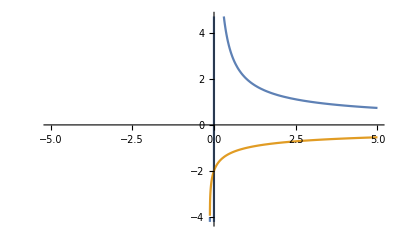

```mathematica
Val1[α2_]= (1+√(1+8 α2))/(2 α2);
Val2[α2_]= (1-√(1+8 α2))/(2 α2);
Plot[{Val1[α2],Val2[α2]},{α2,-5,5}]
```